Data Import

```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210407_sliding_time_windows_and_OR_model"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
datafull=Import["../data/ccm_manipulated_396096.csv",HeaderLines->1];
```

Data with Sliding Time Windows

```mathematica
x=Round@Ceiling[Length@datafull/21,1]
{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,r,s,t,u,v}=Join[Range[x,Length@datafull,x],{Length@datafull}];
data=Join[{Take[datafull,{1,a}]},Flatten[Table[{Take[datafull,{z[[1]]-x/2,z[[2]]-x/2}],Take[datafull,{z[[1]],z[[2]]}]},{z,
Partition[{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,r,s,t,u,v},2,1]}],1]];
win=Length@data
```

18862

41

```mathematica
<<IGraphM`
```

IGraph/M 0.5.1 (October 12, 2020)
Evaluate IGDocumentation[] to get started.

Investigation of Constraints Impact in Time Windows

Fixed Step Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[9,11,win];]
```

{82.4795,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedstep[[1]][[i]],widthdataintimewindowsFixedstep[[2]][[i]],2,7,400,Green],{i,Range@win}];
```

```mathematica
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{4,3,2,3,3,2,3,3,4,3,3,3,2,2,2,2,3,3,3,3,3,2,3,2,3,3,3,3,3,4,2,3,3,3,2,3,3,3,3,3,2}

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{801.343,{{17.9351,24.1336,10.2099},{25.5011,31.3348,16.6943},{23.1159,28.9387,16.8849},{34.43,42.791,24.0656},{21.3336,28.7842,10.2983},{15.8981,21.9229,8.31516},{19.3044,25.0459,13.9656},{26.338,32.9056,19.6941},{25.0225,32.886,15.3915},{34.6087,39.5401,20.9919},{33.9137,41.49,21.3128},{29.3978,36.5431,17.2204},{21.2277,25.0539,14.7383},{39.1516,42.8957,32.8509},{37.7268,41.9981,28.7794},{23.8821,29.2472,16.0662},{29.2101,34.9807,18.4492},{26.787,ComplexInfinity,18.0721},{26.2015,32.7422,16.0945},{30.1327,35.546,22.0603},{36.1136,41.1323,25.5487},{26.0887,30.3846,16.7791},{24.5602,29.8766,9.5955},{13.6073,19.7054,4.03402},{12.312,16.5537,2.00158},{29.4122,37.3087,15.3935},{26.6642,30.3471,15.2937},{25.7088,33.8335,12.5108},{37.8015,42.7069,21.4084},{24.7472,ComplexInfinity,12.3825},{35.8035,42.4221,27.5892},{33.1626,38.732,22.7108},{36.1,40.6707,27.6274},{36.3748,41.9053,25.0076},{38.948,46.371,28.9792},{32.1613,42.4125,19.2742},{29.7392,37.5727,13.8297},{26.6924,33.5993,14.2551},{35.3046,38.0787,24.2317},{53.012,57.3894,37.3792},{45.8767,50.9017,35.1932}}}

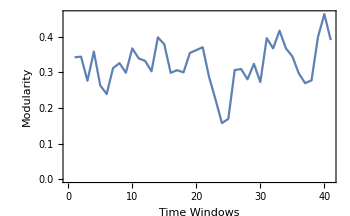
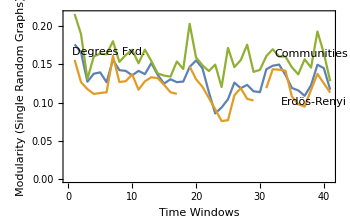
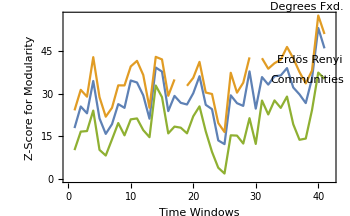

```mathematica
{ListLinePlot[Thread[{Range@win,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->{{0,win+1},MinMax[{modularityvalues,singlerandomerdrenmodularityvalues,singlerandomdegreesfxdmodularityvalues,singlerandomcommmodularityvalues}]}],ListLinePlot[{Thread[{Range@win,singlerandomerdrenmodularityvalues}],Thread[{Range@win,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@win,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{0,win+1},MinMax[{modularityvalues,singlerandomerdrenmodularityvalues,singlerandomdegreesfxdmodularityvalues,singlerandomcommmodularityvalues}]},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]],ListLinePlot[{Thread[{Range@win,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->{{0,win+1},All},PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[10,1,win];]
```

{20.4288,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedstep[[1]][[i]],thicknessdataintimewindowsFixedstep[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win}];
```

```mathematica
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{4,3,2,4,4,5,2,3,3,3,3,3,4,3,2,2,4,6,4,3,3,4,5,4,4,2,4,4,4,4,5,1,1,3,3,3,3,2,2,2,2}

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{256.16,{{0.00587973,ComplexInfinity,-1.24455},{2.45647,3.89335,1.69964},{2.42885,2.90818,2.01213},{-1.8287,ComplexInfinity,-1.35467},{4.66418,7.58887,3.28863},{4.60384,ComplexInfinity,4.21484},{3.35954,3.94711,3.08596},{1.32351,1.73943,0.628496},{0.156722,-0.00928693,-0.663088},{0.2097,0.0886965,0.172772},{-0.080981,0.116941,0.259549},{3.0071,4.80896,2.00685},{2.32015,3.55641,0.92474},{2.10499,2.45206,1.98758},{1.60715,2.91993,1.56281},{-0.00372361,1.82263,0.168206},{2.57417,ComplexInfinity,1.30506},{-0.407226,ComplexInfinity,-0.941266},{2.03931,3.22853,1.77697},{2.95875,3.49042,2.3868},{1.20752,2.17362,0.795013},{2.27312,4.86552,0.682164},{-1.01344,ComplexInfinity,-2.40559},{-0.52583,ComplexInfinity,-0.914984},{0.049107,ComplexInfinity,0.297772},{1.66082,5.28505,0.568374},{0.671124,ComplexInfinity,-0.687005},{1.71725,ComplexInfinity,0.408904},{-0.254967,ComplexInfinity,-0.207875},{0.124358,ComplexInfinity,0.0776945},{-1.20981,ComplexInfinity,-0.94238},{Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate},{3.38623,2.36238,3.2917},{2.46462,1.44739,2.56609},{-1.41974,-1.13584,-1.54404},{0.688623,0.386007,0.438382},{-0.926445,-1.34498,-0.19723},{0.912632,0.757515,0.846483},{3.70818,3.36177,3.13673},{0.35968,1.72031,0.227813}}}

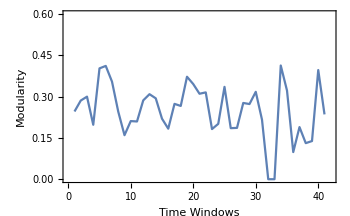
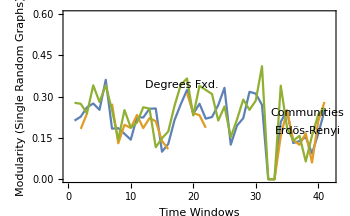
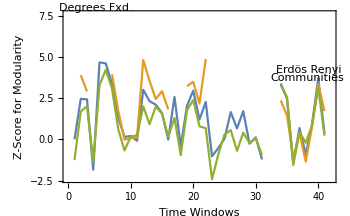

```mathematica
{ListLinePlot[Thread[{Range@win,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->{{0,win+1},{0,0.6}}],ListLinePlot[{Thread[{Range@win,singlerandomerdrenmodularityvalues}],Thread[{Range@win,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@win,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{0,win+1},{0,0.6}},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]],ListLinePlot[{Thread[{Range@win,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->{{0,win+1},All},PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]]}
```

Length Feature

```mathematica
AbsoluteTiming[lengthdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[12,400,win];]
```

{107.014,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[lengthdataintimewindowsFixedstep[[1]][[i]],lengthdataintimewindowsFixedstep[[2]][[i]],2,7,400,RGBColor[1.,0.53,0.2]],{i,Range@win}];
```

```mathematica
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,2,2,2,2,3,4,2,2,2,2,2,3,2,3,2,2,2,2,2,2,2,2,2}

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{2695.74,{{29.0298,35.5979,17.5966},{24.6648,31.4529,12.2024},{37.2005,43.2163,17.6847},{28.9652,35.4922,13.2498},{27.3261,34.6296,10.8346},{31.5431,39.9408,16.78},{31.9278,38.6933,15.8863},{38.9337,43.7244,21.2},{23.9506,28.4119,7.8459},{29.7453,34.5769,13.1476},{43.6284,51.1664,26.5605},{30.1981,35.3246,13.076},{30.3133,34.6838,14.2579},{45.1974,52.5859,27.6564},{47.9136,54.1129,30.6966},{45.5943,50.5683,24.4581},{37.9983,42.182,18.3578},{29.3848,37.5155,12.7524},{31.8655,41.4558,16.1844},{39.1603,47.1436,22.7667},{33.965,39.3603,19.3153},{24.5658,30.0406,10.1432},{21.1021,ComplexInfinity,7.15404},{14.736,ComplexInfinity,-1.48477},{20.7354,24.2564,3.56542},{18.4921,23.2291,3.95447},{16.7775,21.9861,1.64746},{14.7823,18.2045,0.559903},{13.48,17.973,2.35103},{14.3386,19.8226,2.23871},{27.3727,31.2751,14.515},{22.7495,29.6743,8.34344},{35.6979,38.137,20.9072},{37.5047,41.9672,19.6585},{25.9966,31.9785,13.6275},{20.8019,26.9831,9.3314},{18.4977,24.8952,5.24276},{15.9583,20.571,3.53979},{29.1186,34.7873,16.1174},{29.3226,34.7331,14.4932},{25.0303,28.7769,11.7468}}}

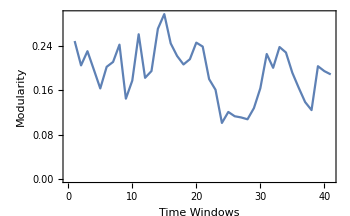
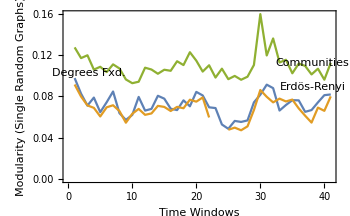
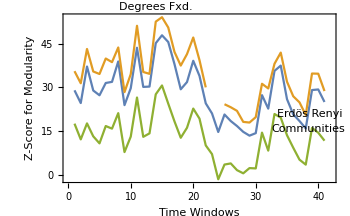

```mathematica
{ListLinePlot[Thread[{Range@win,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->{{0,win+1},MinMax[{modularityvalues,singlerandomerdrenmodularityvalues,singlerandomdegreesfxdmodularityvalues,singlerandomcommmodularityvalues}]}],ListLinePlot[{Thread[{Range@win,singlerandomerdrenmodularityvalues}],Thread[{Range@win,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@win,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{0,win+1},MinMax[{modularityvalues,singlerandomerdrenmodularityvalues,singlerandomdegreesfxdmodularityvalues,singlerandomcommmodularityvalues}]},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]],ListLinePlot[{Thread[{Range@win,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->{{0,win+1},All},PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]]}
```

Weight Feature

```mathematica
AbsoluteTiming[weightdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[11,200,win];]
```

{177.852,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[weightdataintimewindowsFixedstep[[1]][[i]],weightdataintimewindowsFixedstep[[2]][[i]],2,7,400,Red],{i,Range@win}];
```

```mathematica
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{4,3,3,3,3,3,4,3,4,2,3,3,3,3,3,3,3,3,3,3,3,3,2,4,3,3,3,2,2,3,3,3,3,4,3,3,2,2,4,3,3}

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{1966.72,{{9.17433,ComplexInfinity,-1.70331},{4.48315,9.98351,-6.35687},{8.77897,14.3282,-4.12834},{3.54319,7.96151,-7.48007},{4.44464,8.61674,-7.06419},{2.60042,7.29587,-6.2164},{4.24939,9.50533,-6.58649},{4.25349,8.98212,-6.47687},{5.58157,10.7461,-8.46322},{6.01786,11.2368,-3.65108},{9.54937,12.5906,-3.49686},{10.8144,16.5428,-2.45929},{12.8438,18.6806,-1.49802},{9.58541,17.2286,-3.50367},{11.1845,18.2121,-0.709377},{3.82524,9.08162,-6.41406},{5.26702,10.1779,-5.67916},{3.86505,9.73371,-7.00392},{5.77499,10.7825,-3.93125},{11.3086,16.8359,-2.6057},{11.346,16.0116,-1.9961},{14.5106,19.4816,-0.813522},{20.4226,25.6065,5.79103},{6.06058,12.9583,-6.65655},{6.46584,11.5091,-6.2188},{10.884,15.5937,-4.48064},{7.81385,12.6471,-5.45162},{6.50378,9.99302,-3.91768},{17.3433,23.1453,3.82209},{9.55106,13.9486,-0.218374},{7.07213,10.711,-2.53718},{9.977,14.9325,-2.19742},{13.4436,17.5318,-0.175787},{9.16124,14.794,-5.49607},{8.2892,15.0269,-4.3647},{8.89252,14.4622,-3.74829},{7.71516,13.9867,-2.1945},{10.226,15.7627,-1.2618},{6.86926,12.1725,-2.61821},{10.7184,16.8702,-1.05486},{13.9658,19.1903,-0.715471}}}

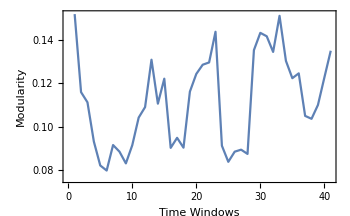
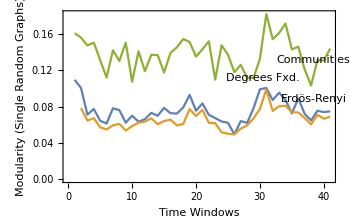
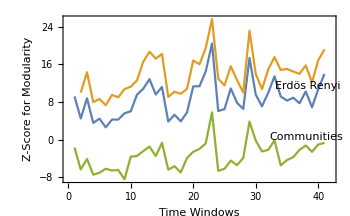

```mathematica
{ListLinePlot[Thread[{Range@win,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->{{0,win+1},MinMax[{modularityvalues,singlerandomerdrenmodularityvalues,singlerandomdegreesfxdmodularityvalues,singlerandomcommmodularityvalues}]}],ListLinePlot[{Thread[{Range@win,singlerandomerdrenmodularityvalues}],Thread[{Range@win,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@win,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{0,win+1},MinMax[{modularityvalues,singlerandomerdrenmodularityvalues,singlerandomdegreesfxdmodularityvalues,singlerandomcommmodularityvalues}]},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]],ListLinePlot[{Thread[{Range@win,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->{{0,win+1},All},PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]]}
```

Fixed Bucket Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[9,85,win];]
```

{9.47604,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedbucket[[1]][[i]],widthdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,Green],{i,Range@win}];
```

```mathematica
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{2,3,2,2,3,3,3,3,2,3,2,3,2,3,2,3,3,2,3,2,2,3,3,2,2,2,3,2,2,3,3,3,3,2,3,3,2,2,3,2,2}

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{1053.76,{{21.4837,29.9389,13.1462},{20.7283,24.0335,6.28902},{15.9954,21.7257,5.24976},{52.205,62.7934,41.9524},{22.7475,28.6075,10.6195},{22.9926,26.6829,9.22781},{18.1183,20.994,7.43109},{29.7148,37.1586,17.8076},{22.0134,28.2237,11.5568},{18.2538,24.0986,8.65908},{33.0973,36.8496,21.1946},{33.3582,39.3147,19.7566},{39.6163,44.7756,28.5466},{31.5866,37.7741,19.8489},{35.9563,44.2693,28.4737},{35.9324,40.9323,24.8707},{21.2866,26.4058,10.1129},{21.8454,28.7547,9.72422},{26.5465,31.5695,16.2262},{36.5273,41.3757,28.3724},{32.8907,35.6686,22.8742},{18.7951,23.2513,5.57516},{12.993,18.5885,2.98762},{7.54895,13.8955,-0.64529},{11.0035,14.9442,2.19931},{28.1362,32.6995,17.3557},{25.5627,31.3903,11.5412},{27.6819,34.1958,16.0931},{15.3174,20.4746,5.92453},{24.002,29.1826,9.15821},{31.963,37.8255,25.7851},{28.1973,32.0861,16.8583},{22.8375,29.4298,11.0068},{41.065,49.8482,33.3666},{22.93,28.8027,13.9057},{15.6876,22.9609,3.0795},{25.4574,29.7798,13.086},{25.2656,34.1375,14.9014},{15.2524,21.5483,4.3484},{32.1059,40.7354,23.2253},{40.492,46.5737,30.7535}}}

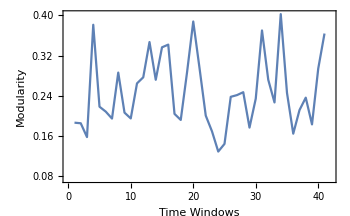
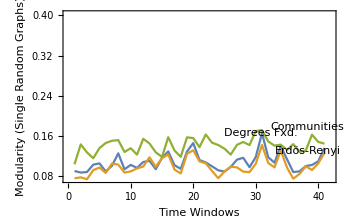
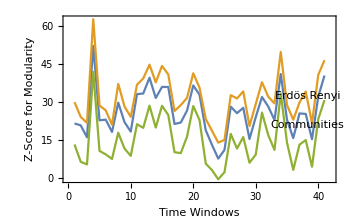

```mathematica
{ListLinePlot[Thread[{Range@win,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->{{0,win+1},MinMax[{modularityvalues,singlerandomerdrenmodularityvalues,singlerandomdegreesfxdmodularityvalues,singlerandomcommmodularityvalues}]}],ListLinePlot[{Thread[{Range@win,singlerandomerdrenmodularityvalues}],Thread[{Range@win,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@win,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{0,win+1},MinMax[{modularityvalues,singlerandomerdrenmodularityvalues,singlerandomdegreesfxdmodularityvalues,singlerandomcommmodularityvalues}]},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]],ListLinePlot[{Thread[{Range@win,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->{{0,win+1},All},PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[10,20,win];]
```

{7.34766,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedbucket[[1]][[i]],thicknessdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win}];
```

```mathematica
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{3,3,4,3,4,4,2,3,4,3,4,3,4,5,4,3,4,4,3,4,3,3,3,3,3,2,3,3,4,3,3,4,4,4,3,4,4,5,5,4,3}

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{286.902,{{2.97657,5.68595,1.17267},{4.89915,5.06916,2.60325},{5.69251,6.09299,4.64238},{-0.300163,0.781249,0.104287},{1.25087,2.65229,-0.322909},{0.562029,0.815257,-1.21751},{5.9135,6.91374,5.08106},{1.01828,2.11083,0.545591},{0.778024,1.85997,-1.08219},{2.61617,3.02956,2.38091},{0.775731,1.55998,0.199297},{2.6821,4.00014,1.7388},{0.407256,1.00887,-0.485522},{1.57142,1.97236,0.732457},{3.37288,2.81608,4.18209},{3.55908,3.40738,3.81089},{0.322044,0.919634,-0.0484739},{0.669659,1.79874,0.1069},{0.865577,1.96199,0.709819},{2.17722,2.2733,2.38077},{1.94029,2.89563,1.57403},{1.02853,3.01474,0.562998},{4.10859,4.51096,3.49665},{3.56796,4.44192,3.61481},{1.11575,2.43639,0.674567},{3.78946,4.55646,3.31934},{0.298531,2.87949,-0.962257},{2.0755,3.51268,1.8376},{0.804488,1.2618,0.556766},{1.70833,3.43076,0.434178},{-1.73959,-0.123885,-1.61959},{3.66336,2.9385,4.05588},{4.17595,3.55754,4.72689},{4.05075,3.7043,4.48526},{4.555,4.44189,4.7522},{3.26413,4.32757,3.15345},{5.25619,4.72295,5.44167},{4.44021,3.89912,5.58788},{6.13408,5.31607,7.16499},{5.72951,5.55375,6.24975},{5.48807,5.22379,3.8895}}}

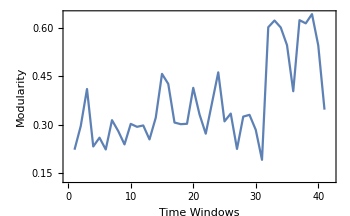
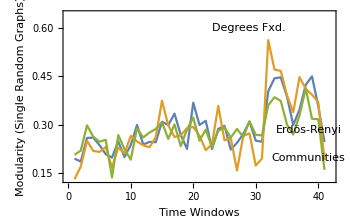
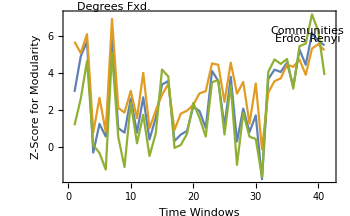

```mathematica
{ListLinePlot[Thread[{Range@win,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->{{0,win+1},MinMax[{modularityvalues,singlerandomerdrenmodularityvalues,singlerandomdegreesfxdmodularityvalues,singlerandomcommmodularityvalues}]}],ListLinePlot[{Thread[{Range@win,singlerandomerdrenmodularityvalues}],Thread[{Range@win,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@win,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{0,win+1},MinMax[{modularityvalues,singlerandomerdrenmodularityvalues,singlerandomdegreesfxdmodularityvalues,singlerandomcommmodularityvalues}]},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]],ListLinePlot[{Thread[{Range@win,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->{{0,win+1},All},PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]]}
```

Length Feature

```mathematica
AbsoluteTiming[lengthdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[12,102,win];]
```

{11.9113,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[lengthdataintimewindowsFixedbucket[[1]][[i]],lengthdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,RGBColor[1.,0.53,0.2]],{i,Range@win}];
```

```mathematica
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,3,2,3,3,3,2,2,2,2,3,2,2,2,2}

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{3174.91,{{22.1215,23.288,0.836139},{45.7415,50.2085,25.0307},{32.0682,36.3735,9.4698},{30.9972,41.6301,13.2594},{40.1063,51.2126,19.5114},{34.3939,40.8692,14.503},{44.1747,47.7406,19.8275},{51.785,56.1676,25.8482},{36.0692,43.5423,12.6228},{30.984,42.1516,13.4301},{63.3838,69.0305,40.4347},{48.1367,55.9904,25.5653},{41.8249,44.1302,19.5039},{67.0685,68.3311,44.0182},{66.269,71.2153,41.0783},{52.8487,63.2107,29.6568},{43.197,48.765,21.6345},{42.4042,45.5848,19.4244},{44.3354,49.778,23.4756},{44.3912,47.3011,24.6907},{44.3225,51.3138,26.105},{29.8502,31.7714,7.43316},{28.6001,28.6132,8.64039},{18.0609,21.6162,0.345918},{23.3983,25.8921,4.18198},{28.2305,33.7621,5.30944},{8.64239,11.1661,-4.86079},{9.17125,13.2217,-4.5658},{20.9413,25.5667,4.09928},{27.0039,32.0819,11.2989},{38.2392,44.6449,17.7724},{30.3334,37.7264,14.874},{46.5656,47.7349,24.9018},{37.9061,43.6727,20.6761},{34.4554,41.7432,16.1144},{38.363,45.7893,22.4082},{18.0655,21.8531,1.1882},{32.1446,37.3431,12.6267},{50.3863,58.4529,30.364},{44.2977,49.2063,25.732},{21.5983,24.7882,6.34321}}}

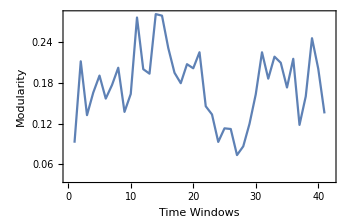
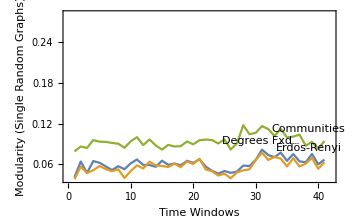
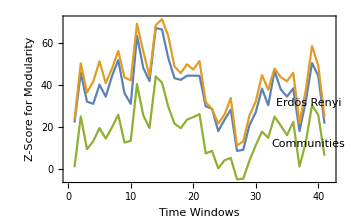

```mathematica
{ListLinePlot[Thread[{Range@win,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->{{0,win+1},MinMax[{modularityvalues,singlerandomerdrenmodularityvalues,singlerandomdegreesfxdmodularityvalues,singlerandomcommmodularityvalues}]}],ListLinePlot[{Thread[{Range@win,singlerandomerdrenmodularityvalues}],Thread[{Range@win,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@win,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{0,win+1},MinMax[{modularityvalues,singlerandomerdrenmodularityvalues,singlerandomdegreesfxdmodularityvalues,singlerandomcommmodularityvalues}]},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]],ListLinePlot[{Thread[{Range@win,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->{{0,win+1},All},PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]]}
```

Weight Feature

```mathematica
AbsoluteTiming[weightdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[11,100,win];]
```

{11.1143,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[weightdataintimewindowsFixedbucket[[1]][[i]],weightdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,Red],{i,Range@win}];
```

```mathematica
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{2,2,2,2,2,2,3,3,2,3,2,2,2,2,2,3,2,2,3,2,2,2,2,3,2,2,2,3,3,3,3,3,2,2,3,2,3,3,3,3,3}

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{2607.54,{{37.6073,39.603,14.5244},{26.4196,30.3593,9.43656},{27.0143,31.4938,10.6738},{20.7949,23.5472,4.86959},{15.3959,20.2409,1.51243},{11.3453,15.8403,-1.286},{10.9064,13.8071,-4.00145},{20.7174,23.9138,2.69284},{23.1872,29.4417,5.84352},{9.79181,13.5144,-3.6643},{11.127,12.6164,-1.83388},{26.9233,31.2857,7.68073},{15.1844,18.3557,0.503985},{6.43345,8.5392,-5.23392},{21.9061,25.3504,6.1096},{27.7908,32.1767,6.9791},{18.6338,21.4758,1.91945},{19.5758,23.6195,2.71153},{18.6528,22.8899,3.46456},{18.0934,22.8789,3.5577},{9.46615,10.7646,-1.83316},{18.6887,22.0893,3.28699},{21.6496,22.7216,4.71327},{11.7511,16.2801,-3.73565},{12.848,17.0936,-1.66042},{22.4789,29.1108,3.32125},{11.0652,15.398,-2.49948},{12.1126,15.012,-3.65889},{12.9752,17.1028,-1.01251},{18.9729,23.1426,1.94429},{14.4313,20.1917,1.44917},{18.387,23.2108,1.12337},{22.7008,23.3935,6.65081},{21.1774,24.7452,6.81922},{16.5057,20.7819,-0.0559239},{15.4043,19.8105,2.80805},{20.3733,26.1442,2.26705},{18.4538,23.2197,3.3672},{9.31869,12.5119,-4.18035},{20.1988,24.4695,4.00246},{21.7837,23.9751,2.98396}}}

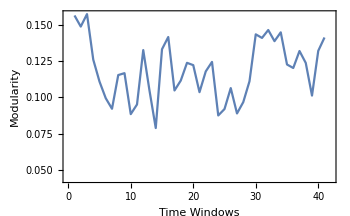
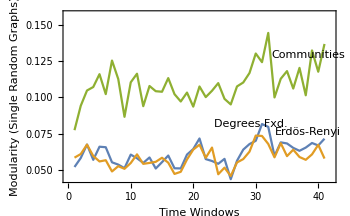
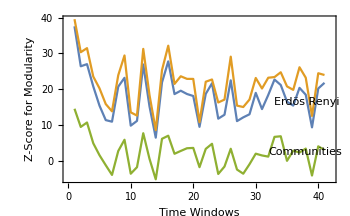

```mathematica
{ListLinePlot[Thread[{Range@win,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->{{0,win+1},MinMax[{modularityvalues,singlerandomerdrenmodularityvalues,singlerandomdegreesfxdmodularityvalues,singlerandomcommmodularityvalues}]}],ListLinePlot[{Thread[{Range@win,singlerandomerdrenmodularityvalues}],Thread[{Range@win,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@win,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{0,win+1},MinMax[{modularityvalues,singlerandomerdrenmodularityvalues,singlerandomdegreesfxdmodularityvalues,singlerandomcommmodularityvalues}]},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]],ListLinePlot[{Thread[{Range@win,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->{{0,win+1},All},PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]]}
```